```mathematica
f[z_]:= 1 - β^2/2 z^2 - (1 - β^2/2+μ^2/4)z^3+μ^2/4 z^4;
h[z_]:= 1;
```

```mathematica
SFiniteIntegrant = 1/z^2(√(h[z]/(1 - z^4/zstar^4 h[zstar]^2/h[z]^2))1/(√f[z])-1)
```

(-1+(√(1/(1-z^4/zstar^4)))/(√(1-(z^2 β^2)/2+(z^4 μ^2)/4-z^3 (1-β^2/2+μ^2/4))))/z^2

```mathematica
SFinite0[zz_,ββ_, μμ_] := NIntegrate[SFiniteIntegrant /. {β -> ββ, μ->μμ, zstar -> zz},  {z, 0, zz}]
```

```mathematica
SFinite[zz_, ββ_, μμ_] := SFinite0[zz, ββ, μμ] - 1/zz
```

```mathematica
lIntegrand=1/(√(h[α]^2/h[zstar]^2 zstar^4/α^4-1))1/(√(h[α]f[α]))
```

1/(√(-1+zstar^4/α^4) √(1-(α^2 β^2)/2+(α^4 μ^2)/4-α^3 (1-β^2/2+μ^2/4)))

```mathematica
l[zz_, ββ_, μμ_] := 2 NIntegrate[lIntegrand/.{β -> ββ, μ->μμ,zstar->zz}, {α,0,zz}]
```

```mathematica
l[0.5, 0.5, 0.5]
```

0.631027

```mathematica
zStarSpacing = 0.0001;
```

```mathematica
lTable0 = Table[l[z, 0.5, 0.5], {z,zStarSpacing,1,zStarSpacing}];
SFiniteTable0 = Table[SFinite[z, 0.5, 0.5], {z,zStarSpacing,1,zStarSpacing}];
lTable1 = Table[l[z, 1.0, 0.5], {z,zStarSpacing,1,zStarSpacing}];
SFiniteTable1 = Table[SFinite[z, 1.0, 0.5], {z,zStarSpacing,1,zStarSpacing}];
lTable2 = Table[l[z, 0.5, 1.0], {z,zStarSpacing,1,zStarSpacing}];
SFiniteTable2 = Table[SFinite[z, 0.5, 1.0], {z,zStarSpacing,1,zStarSpacing}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 10.5869 and 0.442559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 11.605 and 0.408368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 11.3444 and 0.457096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 12.4883 and 0.393231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.9999465496780171902568325192905973608503700233995914459228515625}. NIntegrate obtained 14.2665 and 3.96136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 11.7257 and 0.167065 for the integral and error estimates.

```mathematica
lStarTable = Table[z, {z,zStarSpacing,1,zStarSpacing}];
```

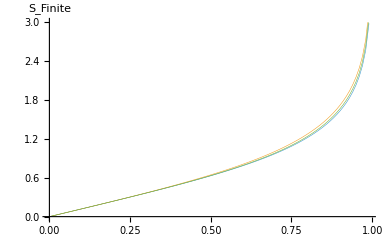

```mathematica
plotPointsStep = 100;
ListPlot[{Transpose@{lStarTable, lTable0}[[All, ;;;;plotPointsStep]], Transpose@{lStarTable, lTable1}[[All, ;;;;plotPointsStep]], Transpose@{lStarTable, lTable2}[[All, ;;;;plotPointsStep]]}, Joined->True, AxesLabel->{"", "S_Finite"}, PlotStyle->Thickness[0.001], PlotRange->{0, 3}]
```

```mathematica
fitFunction = Sum[Subscript[c, i] l^i, {i, -1, 5}]
```

(c_-1)/l+c_0+l c_1+l^2 c_2+l^3 c_3+l^4 c_4+l^5 c_5

```mathematica
fit1 = FindFit[(Transpose@{lTable0, SFiniteTable0}),fitFunction, Table[Subscript[c, i], {i,-1,5}], l]
```

{c_-1→-0.71777,c_0→0.000392441,c_1→0.0389882,c_2→0.150646,c_3→-0.0280708,c_4→0.00251985,c_5→-0.0000699596}

```mathematica
fit2 = FindFit[(Transpose@{lTable1, SFiniteTable1}),fitFunction, Table[Subscript[c, i], {i,-1,5}], l]
```

{c_-1→-0.71777,c_0→0.0000370986,c_1→0.180647,c_2→0.0847186,c_3→-0.0132294,c_4→0.00103806,c_5→-0.0000260719}

```mathematica
fit3 = FindFit[(Transpose@{lTable2, SFiniteTable2}),fitFunction, Table[Subscript[c, i], {i,-1,5}], l]
```

{c_-1→-0.71777,c_0→-0.00104693,c_1→0.0511991,c_2→0.154044,c_3→-0.0302094,c_4→0.0027256,c_5→-0.0000645584}

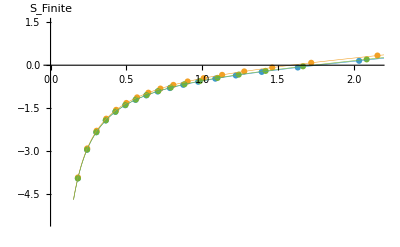

```mathematica
plotPointsStep = 500;
p1 = ListPlot[{Transpose@{lTable0, SFiniteTable0}[[All, ;;;;plotPointsStep]], Transpose@{lTable1, SFiniteTable1}[[All, ;;;;plotPointsStep]], Transpose@{lTable2, SFiniteTable2}[[All, ;;;;plotPointsStep]]}, Joined->False, AxesLabel->{"", "S_Finite"}, PlotStyle->Thickness[0.01], PlotRange->{-5.5, 1.5}];
p2 = Plot[{fitFunction/.fit1, fitFunction/.fit2, fitFunction/.fit3}, {l, 0, 2.2}, PlotStyle->Thickness[0.001]];
Show[p1, p2]
```